```mathematica
(*g:=a+b*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]*)
g:=Sqrt[a b]+Sqrt[a b]*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]
h :=(g/.{Subscript[z, j]->Subscript[z, j],Subscript[z, k]->Subscript[z, k]})(g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->1/Subscript[z, j]})/
((g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->Subscript[z, j]})(g/.{Subscript[z, j]->1/Subscript[z, j],Subscript[z, k]->Subscript[z, k]}))
h1:=h/.{Subscript[z, j]->Subscript[z, 1],Subscript[z, k]->Subscript[z, 2]}
h2:=h/.{Subscript[z, j]->Subscript[z, 2],Subscript[z, k]->Subscript[z, 1]}
f1:=(Subscript[z, 1]^8 - h1)/.{a->1,b->2}
f2:=(Subscript[z, 2]^8- h2)/.{a->1,b->2}
(*roots = FindRoot[{f1==0,f2==0}, {{Subscript[z, 1],-1}, {Subscript[z, 2],3}}]*)
roots = Solve[{f1==0,f2==0}, {Subscript[z, 1],Subscript[z, 2]}]//N
```

{{z_1→-1.,z_2→-1.},{z_1→-1.,z_2→1.},{z_1→0.,z_2→0.},{z_1→1.,z_2→-1.},{z_1→1.,z_2→1.},{z_1→0.332423+0.443604 ⅈ,z_2→0.332423-0.443604 ⅈ},{z_1→0.332423+0.443604 ⅈ,z_2→1.08179+1.4436 ⅈ},{z_1→1.08179-1.4436 ⅈ,z_2→0.332423-0.443604 ⅈ},{z_1→1.08179-1.4436 ⅈ,z_2→1.08179+1.4436 ⅈ},{z_1→0.332423-0.443604 ⅈ,z_2→0.332423+0.443604 ⅈ},{z_1→0.332423-0.443604 ⅈ,z_2→1.08179-1.4436 ⅈ},{z_1→1.08179+1.4436 ⅈ,z_2→0.332423+0.443604 ⅈ},{z_1→1.08179+1.4436 ⅈ,z_2→1.08179-1.4436 ⅈ},{z_1→-0.644484-0.764618 ⅈ,z_2→0.29093-0.956744 ⅈ},{z_1→-0.644484-0.764618 ⅈ,z_2→0.29093+0.956744 ⅈ},{z_1→-0.644484+0.764618 ⅈ,z_2→0.29093-0.956744 ⅈ},{z_1→-0.644484+0.764618 ⅈ,z_2→0.29093+0.956744 ⅈ},{z_1→0.29093-0.956744 ⅈ,z_2→-0.644484+0.764618 ⅈ},{z_1→0.29093-0.956744 ⅈ,z_2→-0.644484-0.764618 ⅈ},{z_1→0.29093+0.956744 ⅈ,z_2→-0.644484-0.764618 ⅈ},{z_1→0.29093+0.956744 ⅈ,z_2→-0.644484+0.764618 ⅈ},{z_1→-0.698539-0.715572 ⅈ,z_2→1.},{z_1→-0.698539+0.715572 ⅈ,z_2→1.},{z_1→0.759199-0.650858 ⅈ,z_2→1.},{z_1→0.759199+0.650858 ⅈ,z_2→1.},{z_1→0.301461-0.953478 ⅈ,z_2→-1.},{z_1→0.301461+0.953478 ⅈ,z_2→-1.},{z_1→0.311863,z_2→-1.},{z_1→3.20654,z_2→-1.},{z_1→0.779307,z_2→1.},{z_1→1.28319,z_2→1.},{z_1→-0.614912-0.788596 ⅈ,z_2→-1.},{z_1→-0.614912+0.788596 ⅈ,z_2→-1.},{z_1→0.331123,z_2→-1.},{z_1→3.02002,z_2→-1.},{z_1→0.029411-0.999567 ⅈ,z_2→1.},{z_1→0.029411+0.999567 ⅈ,z_2→1.},{z_1→-0.620302-0.784363 ⅈ,z_2→-0.620302+0.784363 ⅈ},{z_1→-0.620302-0.784363 ⅈ,z_2→-0.620302-0.784363 ⅈ},{z_1→-0.620302+0.784363 ⅈ,z_2→-0.620302-0.784363 ⅈ},{z_1→-0.620302+0.784363 ⅈ,z_2→-0.620302+0.784363 ⅈ},{z_1→0.232899-0.972501 ⅈ,z_2→0.232899+0.972501 ⅈ},{z_1→0.232899-0.972501 ⅈ,z_2→0.232899-0.972501 ⅈ},{z_1→0.232899+0.972501 ⅈ,z_2→0.232899-0.972501 ⅈ},{z_1→0.232899+0.972501 ⅈ,z_2→0.232899+0.972501 ⅈ},{z_1→0.917733-0.397198 ⅈ,z_2→0.917733+0.397198 ⅈ},{z_1→0.917733-0.397198 ⅈ,z_2→0.917733-0.397198 ⅈ},{z_1→0.917733+0.397198 ⅈ,z_2→0.917733-0.397198 ⅈ},{z_1→0.917733+0.397198 ⅈ,z_2→0.917733+0.397198 ⅈ},{z_1→1.,z_2→-0.698539-0.715572 ⅈ},{z_1→1.,z_2→-0.698539+0.715572 ⅈ},{z_1→1.,z_2→0.759199-0.650858 ⅈ},{z_1→1.,z_2→0.759199+0.650858 ⅈ},{z_1→-1.,z_2→0.301461-0.953478 ⅈ},{z_1→-1.,z_2→0.301461+0.953478 ⅈ},{z_1→-1.,z_2→0.311863},{z_1→-1.,z_2→3.20654},{z_1→1.,z_2→0.779307},{z_1→1.,z_2→1.28319},{z_1→-1.,z_2→-0.614912-0.788596 ⅈ},{z_1→-1.,z_2→-0.614912+0.788596 ⅈ},{z_1→-1.,z_2→0.331123},{z_1→-1.,z_2→3.02002},{z_1→1.,z_2→0.029411-0.999567 ⅈ},{z_1→1.,z_2→0.029411+0.999567 ⅈ}}

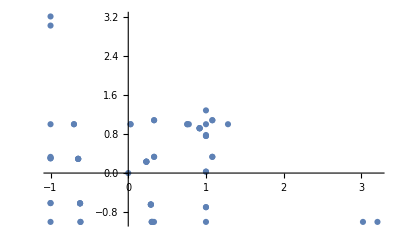

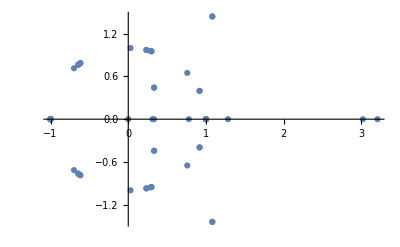

```mathematica
zvals := {Re[Subscript[z, 1]],Re[Subscript[z, 2]]}/.roots
ListPlot[zvals]
zvals := {Re[Subscript[z, 2]],Im[Subscript[z, 2]]}/.roots
ListPlot[zvals]
```

```mathematica
a=1;b=2;
lam[z_]:=Piecewise[{{0,Abs[Re[z]]==1}}, -a-b+2Sqrt[a b]Re[z]]
lamd[x_, y_]:=Piecewise[{{0, lam[x]lam[y]==0||Abs[Re[x]-Re[y]]<10^-6}}, lam[x]+lam[y]]
ev=lamd[Subscript[z, 1], Subscript[z, 2]]/.roots
```

{0,0,0,0,0,0,-2.,-2.,0,0,-2.,-2.,0,-7.,-7.,-7.,-7.,-7.,-7.,-7.,-7.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

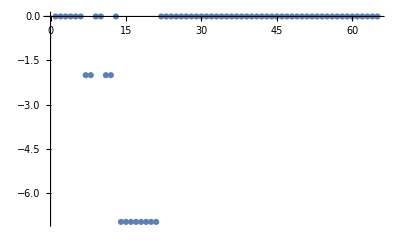

```mathematica
ListPlot[ev]
```

```mathematica
M := Transpose[{{-a, a, 0, 0, 0, 0}, {b, -2*a-b, a, a, 0, 0}, {0, b, -a-b, 0, a, 0}, {0, b, 0, -a-b, a, 0},
 {0, 0, b, b, -a-2*b, a},{0, 0, 0, 0, b, -b}}]
Eigensystem[M]
Eigenvalues[M/.{a->1, b->2}]//N
```

{{-7,-5,-3,-2,-1,0},{{2,-6,4,4,-5,1},{-4,8,-1,-1,-3,1},{0,0,-1,1,0,0},{2,-1,-1,-1,0,1},{-4,0,1,1,1,1},{16,8,4,4,2,1}}}

{-7.,-5.,-3.,-2.,-1.,0.}

```mathematica
(*g:=a+b*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]*)
g:=Sqrt[a b]+Sqrt[a b]*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]
h :=(g/.{Subscript[z, j]->Subscript[z, j],Subscript[z, k]->Subscript[z, k]})(g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->1/Subscript[z, j]})/
((g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->Subscript[z, j]})(g/.{Subscript[z, j]->1/Subscript[z, j],Subscript[z, k]->Subscript[z, k]}))
h1:=h/.{Subscript[z, j]->Subscript[z, 1],Subscript[z, k]->Subscript[z, 2]}
h2:=h/.{Subscript[z, j]->Subscript[z, 2],Subscript[z, k]->Subscript[z, 1]}
f1:=(Subscript[z, 1]^6 - h1)/.{a->1,b->2}
f2:=(Subscript[z, 2]^6- h2)/.{a->1,b->2}
(*roots = FindRoot[{f1==0,f2==0}, {{Subscript[z, 1],-1}, {Subscript[z, 2],3}}]*)
roots = Solve[{f1==0,f2==0}, {Subscript[z, 1],Subscript[z, 2]}]//N
a=1;b=2;
lam[z_]:=Piecewise[{{0,Abs[Re[z]]==1}}, -a-b+2Sqrt[a b]Re[z]]
lamd[x_, y_]:=Piecewise[{{0, lam[x]lam[y]==0||Abs[Re[x]-Re[y]]<10^-6}}, lam[x]+lam[y]]
ev=lamd[Subscript[z, 1], Subscript[z, 2]]/.roots
```

{{z_1→-1.,z_2→-1.},{z_1→-1.,z_2→1.},{z_1→0.,z_2→0.},{z_1→1.,z_2→-1.},{z_1→1.,z_2→1.},{z_1→0.56066-0.828046 ⅈ,z_2→1.},{z_1→0.56066+0.828046 ⅈ,z_2→1.},{z_1→0.36247,z_2→-1.},{z_1→2.75885,z_2→-1.},{z_1→0.831127-0.556083 ⅈ,z_2→0.831127-0.556083 ⅈ},{z_1→0.831127-0.556083 ⅈ,z_2→0.831127+0.556083 ⅈ},{z_1→0.831127+0.556083 ⅈ,z_2→0.831127+0.556083 ⅈ},{z_1→0.831127+0.556083 ⅈ,z_2→0.831127-0.556083 ⅈ},{z_1→-0.300797-0.953688 ⅈ,z_2→-0.300797+0.953688 ⅈ},{z_1→-0.300797-0.953688 ⅈ,z_2→-0.300797-0.953688 ⅈ},{z_1→-0.300797+0.953688 ⅈ,z_2→-0.300797-0.953688 ⅈ},{z_1→-0.300797+0.953688 ⅈ,z_2→-0.300797+0.953688 ⅈ},{z_1→-0.27272-0.962093 ⅈ,z_2→-1.},{z_1→-0.27272+0.962093 ⅈ,z_2→-1.},{z_1→0.296733,z_2→-1.},{z_1→3.37003,z_2→-1.},{z_1→-0.480318-0.877095 ⅈ,z_2→1.},{z_1→-0.480318+0.877095 ⅈ,z_2→1.},{z_1→0.751781,z_2→1.},{z_1→1.33017,z_2→1.},{z_1→1.,z_2→0.56066-0.828046 ⅈ},{z_1→1.,z_2→0.56066+0.828046 ⅈ},{z_1→-1.,z_2→0.36247},{z_1→-1.,z_2→2.75885},{z_1→-1.,z_2→-0.27272-0.962093 ⅈ},{z_1→-1.,z_2→-0.27272+0.962093 ⅈ},{z_1→-1.,z_2→0.296733},{z_1→-1.,z_2→3.37003},{z_1→1.,z_2→-0.480318-0.877095 ⅈ},{z_1→1.,z_2→-0.480318+0.877095 ⅈ},{z_1→1.,z_2→0.751781},{z_1→1.,z_2→1.33017}}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*g:=Sqrt[a b]+Sqrt[a b]*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]*)
g:=a+b*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]
h :=(g/.{Subscript[z, j]->Subscript[z, j],Subscript[z, k]->Subscript[z, k]})/(g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->Subscript[z, j]})
h1:=h/.{Subscript[z, j]->Subscript[z, 1],Subscript[z, k]->Subscript[z, 2]}
h2:=h/.{Subscript[z, j]->Subscript[z, 2],Subscript[z, k]->Subscript[z, 1]}
f1:=(Subscript[z, 1]^4 + h1)/.{a->1,b->2}
f2:=(Subscript[z, 2]^4+ h2)/.{a->1,b->2}
(*roots = FindRoot[{f1==0,f2==0}, {{Subscript[z, 1],-1}, {Subscript[z, 2],3}}]*)
roots = Solve[{f1==0,f2==0}, {Subscript[z, 1],Subscript[z, 2]}]//N
a=1;b=2;
lam[z_]:=Piecewise[{{0,Abs[Re[z]]==1}}, -a-b+a/z + b z]
lamd[x_, y_]:=Piecewise[{{0, lam[x]lam[y]==0||Abs[Re[x]-Re[y]]<10^-6}}, Re[lam[x]+lam[y]]]
ev=lamd[Subscript[z, 1], Subscript[z, 2]]/.roots
```

{{z_1→-0.707107-0.707107 ⅈ,z_2→-0.707107-0.707107 ⅈ},{z_1→0.707107+0.707107 ⅈ,z_2→0.707107+0.707107 ⅈ},{z_1→-0.5-0.866025 ⅈ,z_2→-0.5+0.866025 ⅈ},{z_1→-0.5+0.866025 ⅈ,z_2→-0.5-0.866025 ⅈ},{z_1→0.707107-0.707107 ⅈ,z_2→0.707107-0.707107 ⅈ},{z_1→-0.707107+0.707107 ⅈ,z_2→-0.707107+0.707107 ⅈ},{z_1→-0.414214,z_2→2.41421},{z_1→2.41421,z_2→-0.414214},{z_1→-0.618034,z_2→1.61803},{z_1→1.61803,z_2→-0.618034},{z_1→-0.0944862+0.760772 ⅈ,z_2→1.29449-0.160772 ⅈ},{z_1→1.29449-0.160772 ⅈ,z_2→-0.0944862+0.760772 ⅈ},{z_1→-0.0944862-0.760772 ⅈ,z_2→1.29449+0.160772 ⅈ},{z_1→1.29449+0.160772 ⅈ,z_2→-0.0944862-0.760772 ⅈ}}

{0,0,0,0,0,0,-4.,-4.,-5.,-5.,-3.,-3.,-3.,-3.}

```mathematica
M := {{-a-b, b, 0, 0, a, 0}, {a, -2a-2b, b, b, 0, a}, {0, a, -a-b, 0, b, 0}, {0, a, 0, -a-b, b, 0},{b, 0, a, a, -2a-2b, b},{0, b, 0, 0, a, -a-b}}
Eigenvalues[M/.{a->1, b->2}]//N
M := {{-a-b, b, 0, a}, {a, -a-b, b, 0}, {0, a, -a-b, b}, { b, 0,a, -a-b}}
Re[Eigenvalues[M/.{a->1, b->2}]//N]
```

{-9.,-5.,-4.,-3.,-3.,0.}

{-6.,-3.,-3.,0.}

```mathematica
Solve[2Cot[2k]-Cot[k/2]+Cot[(s-k)/2]==0, k]/.{s->1}//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→-0.377598+2.66454×10^-15 ⅈ},{k→0.377598-2.66454×10^-15 ⅈ},{k→-5.90559-2.66454×10^-15 ⅈ},{k→5.90559+2.66454×10^-15 ⅈ},{k→-4.40829+6.21725×10^-15 ⅈ},{k→4.40829-6.21725×10^-15 ⅈ},{k→-1.8749-6.21725×10^-15 ⅈ},{k→1.8749+6.21725×10^-15 ⅈ},{k→-2.2525+1.00753×10^-14 ⅈ},{k→2.2525-1.00753×10^-14 ⅈ},{k→-4.03069-1.0103×10^-14 ⅈ},{k→4.03069+1.0103×10^-14 ⅈ}}

```mathematica
g:=Sqrt[a b]+Sqrt[a b]Exp[I(Subscript[p, j]+Subscript[p, k])]-(a+b)Exp[I Subscript[p, j]]
h :=(g/.{Subscript[p, j]->Subscript[p, j],Subscript[p, k]->Subscript[p, k]})/(g/.{Subscript[p, j]->Subscript[p, k],Subscript[p, k]->Subscript[p, j]})
(*h :=(g/.{Subscript[p, j]->Subscript[p, j],Subscript[p, k]->Subscript[p, k]})(g/.{Subscript[p, j]->Subscript[p, k],Subscript[p, k]->-Subscript[p, j]})/
((g/.{Subscript[p, j]->Subscript[p, k],Subscript[p, k]->Subscript[p, j]})(g/.{Subscript[p, j]->-Subscript[p, j],Subscript[p, k]->Subscript[p, k]}))*)
h1:=h/.{Subscript[p, j]->Subscript[p, 1],Subscript[p, k]->Subscript[p, 2]}
h2:=h/.{Subscript[p, j]->Subscript[p, 2],Subscript[p, k]->Subscript[p, 1]}
Re[(Exp[I 4 Subscript[p, 1]] + h1)/.{a->1,b->2}]
ComplexExpand[%]
(*f2:=ComplexExpand[Re[(Exp[I 4 Subscript[p, 2]]+ h2)/.{a->1,b->2}]]*)
Simlify[%]
(*roots := Solve[{f1==0,f2==0}, {Subscript[p, 1],Subscript[p, 2]}]//N
ev:=(2Sqrt[a b](Cos[Subscript[p, 1]]+Cos[Subscript[p, 2]])-2(a+b))/.{a->1, b->2}/.roots
Re[ev]*)
```

Re[ⅇ^(4 ⅈ p_1)+(√2-3 ⅇ^(ⅈ p_1)+√2 ⅇ^(ⅈ (p_1+p_2)))/(√2-3 ⅇ^(ⅈ p_2)+√2 ⅇ^(ⅈ (p_1+p_2)))]

Cos[4 p_1]+2/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Cos[p_1])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Cos[p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(9 Cos[p_1] Cos[p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(4 Cos[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Cos[p_1] Cos[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Cos[p_2] Cos[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(2 Cos[p_1+p_2]^2)/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(9 Sin[p_1] Sin[p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Sin[p_1] Sin[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Sin[p_2] Sin[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(2 Sin[p_1+p_2]^2)/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)

Simlify[Cos[4 p_1]+2/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Cos[p_1])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Cos[p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(9 Cos[p_1] Cos[p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(4 Cos[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Cos[p_1] Cos[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Cos[p_2] Cos[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(2 Cos[p_1+p_2]^2)/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(9 Sin[p_1] Sin[p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Sin[p_1] Sin[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)-(3 √2 Sin[p_2] Sin[p_1+p_2])/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)+(2 Sin[p_1+p_2]^2)/((√2-3 Cos[p_2]+√2 Cos[p_1+p_2])^2+(-3 Sin[p_2]+√2 Sin[p_1+p_2])^2)]

```mathematica
f:=(1-2 ⅇ^(ⅈ Subscript[p, 1])+ⅇ^(ⅈ ( Subscript[p, 1]+ Subscript[p, 2])))/(1-2 ⅇ^(ⅈ Subscript[p, 2])+ⅇ^(ⅈ (Subscript[p, 1]+ Subscript[p, 2])))
g:=Refine[f,Subscript[p, 1]∈Reals&&Subscript[p, 2]∈Reals]
h:=ExpToTrig[g]
Re[h]
```

Re[(1-2 Cos[p_1]+Cos[p_1+p_2]-2 ⅈ Sin[p_1]+ⅈ Sin[p_1+p_2])/(1-2 Cos[p_2]+Cos[p_1+p_2]-2 ⅈ Sin[p_2]+ⅈ Sin[p_1+p_2])]